```mathematica
Remove["Global`*"];
Off[General::Spell1];
ClearAll["Global `*"];
```

```mathematica
(*Factorizar el número M=15*)
M=15;
(*x es el número por el que se multiplicará en el algoritmo*)
x=RandomInteger[{2,M-2}]
GCD[x,M]==1
```

7

True

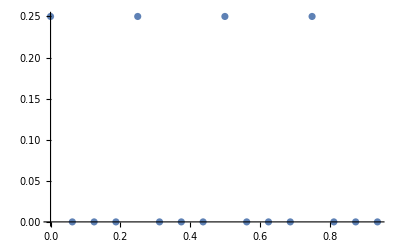

```mathematica
(*Los |0> y |1>*)
Subscript[ket, 0]={{1},{0}};
Subscript[ket, 1]={{0},{1}};

(*El operador identidad*)
Id=IdentityMatrix[2];

(*Las matrices de Pauli*)
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];

(*La compuerta de Hadamard*)
H=HadamardMatrix[2];

(*Los proyectores de la base computacional*)
Subscript[P, 0]=Subscript[ket, 0].ConjugateTranspose[Subscript[ket, 0]];
Subscript[P, 1]=Subscript[ket, 1].ConjugateTranspose[Subscript[ket, 1]];

(*Operador de cambio de fase*)
R[ϕ_]:=Subscript[P, 0] + ⅇ^(ⅈ ϕ) Subscript[P, 1];

(*Compuertas condicionales*)
CNOT=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],X];
CR[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],R[ϕ]];
CR13[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,R[ϕ]];

(*Ket general de la base computacional de dimensión 16*)
ket[n_]:=Table[{n==i-1},{i,1,16}]/.{True->1,False->0};

(*Operador de multiplicación módulo*)
Urp[x_,N_]:=Sum[ket[Mod[x i,N]].ConjugateTranspose[ket[i]],{i,0,N-1}]+Sum[ket[i].ConjugateTranspose[ket[i]],{i,N,15}];

(*Matriz de densidad*)
ρ[ψ_]:=ψ.ConjugateTranspose[ψ];

(*Operador para la estimación de fase: Operador de multiplicación por 7 módulo 15*)
U=Urp[x,M];

(*Preparando el estado inicial*)
ψ0=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0]];
ψ0=N[KroneckerProduct[H,H,H,H].ψ0];
ψ=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 1]];

ψt=N[KroneckerProduct[ψ0,ψ]];

(*Estimación de fase*)
ψt=N[(KroneckerProduct[Id,Id,Id,Subscript[P, 0],Id,Id,Id,Id]+KroneckerProduct[Id,Id,Id,Subscript[P, 1],U]).ψt];
ψt=N[(KroneckerProduct[Id,Id,Subscript[P, 0],Id,Id,Id,Id,Id]+KroneckerProduct[Id,Id,Subscript[P, 1],Id,MatrixPower[U,2]]).ψt];
ψt=N[(KroneckerProduct[Id,Subscript[P, 0],Id,Id,Id,Id,Id,Id]+KroneckerProduct[Id,Subscript[P, 1],Id,Id,MatrixPower[U,2^2]]).ψt];
ψt=N[(KroneckerProduct[Subscript[P, 0],Id,Id,Id,Id,Id,Id,Id]+KroneckerProduct[Subscript[P, 1],Id,Id,Id,MatrixPower[U,2^3]]).ψt];

(*QFT^-1*)
ψt=N[KroneckerProduct[ConjugateTranspose[FourierMatrix[2^4]],Id,Id,Id,Id].ψt];

(*Medidas*)
For[i=0,i<16,i++,sub0=Mod[i,2];sub1=Which[i==0,0,Mod[i,2]==0&&sub1==0,1,Mod[i,2]==0&&sub1==1,0,True,sub1];sub2=Which[i==0,0,Mod[i,2^2]==0&&sub2==0,1,Mod[i,2^2]==0&&sub2==1,0,True,sub2];sub3=Which[i==0,0,Mod[i,2^3]==0&&sub3==0,1,Mod[i,2^3]==0&&sub3==1,0,True,sub3];Subscript[ψt, i]=N[KroneckerProduct[Subscript[P, sub3],Subscript[P, sub2],Subscript[P, sub1],Subscript[P, sub0],Id,Id,Id,Id].ψt];Subscript[ψt, i]=N[ConjugateTranspose[Subscript[ψt, i]].Subscript[ψt, i]];]

(*Organizar resultados de las medidas y graficar*)
L=Table[{i,i/2^4,Subscript[ψt, i][[1,1]]},{i,0,31}];
ListPlot[Table[{N[i/2^4],Subscript[ψt, i][[1,1]]},{i,0,15}],PlotRange->All]
```

```mathematica
(*Procesar medidas para tener la factorización*)
(*Fracciones continuas*)
L1=Table[{Denominator[FromContinuedFraction[ContinuedFraction[Transpose[L][[2,i]]]]],L[[i,3]]},{i,1,16}];
For[i=1,i≤Dimensions[L1][[1]],i++,For[j=1,j≤Dimensions[L1][[1]],j++,If[L1[[i,1]]==L1[[j,1]]&&i≠j,L1[[i,2]]+=L1[[j,2]];L1=Drop[L1,{j}];]]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[OddQ[L1[[i,1]]],L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[Mod[x^L1[[i,1]],M]≠1,L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[GCD[x^(L1[[1,1]]/2),M]==M-1,L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,L1[[i,2]]=L1[[i,2]]/Sum[L1[[j,2]],{j,1,Dimensions[L1][[1]]}];]
L2=Table[{GCD[x^(L1[[i,1]]/2)+1,M],L1[[i,2]]},{i,1,Dimensions[L1][[1]]}];
L3=Table[{GCD[x^(L1[[i,1]]/2)-1,M],L1[[i,2]]},{i,1,Dimensions[L1][[1]]}];
```

{{16,5.20001×10^-33+0. ⅈ},{8,6.16298×10^-33+0. ⅈ},{4,1.+0. ⅈ}}

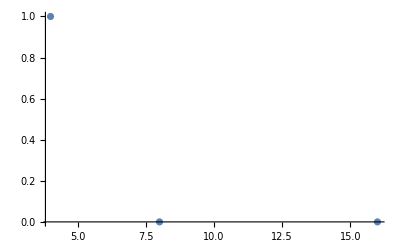

```mathematica
(*Graficar probabilidad de cada posible orden estimado*)
L1
ListPlot[L1]
```

{{1,5.20001×10^-33+0. ⅈ},{1,6.16298×10^-33+0. ⅈ},{5,1.+0. ⅈ}}

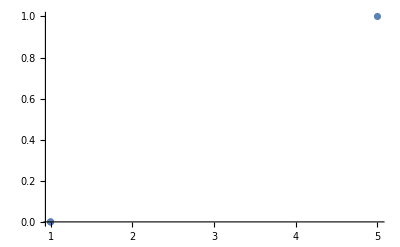

{{15,5.20001×10^-33+0. ⅈ},{15,6.16298×10^-33+0. ⅈ},{3,1.+0. ⅈ}}

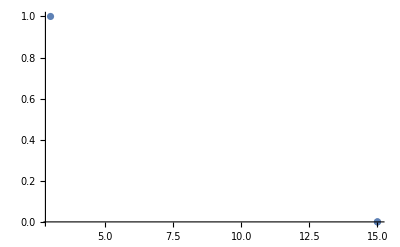

```mathematica
(*Graficar la probabilidad de cada posible factorización hallada*)
L2
ListPlot[L2]
L3
ListPlot[L3]
```